## Wavelength Calibration for the LISA Spectrograph - General Template Huib Henrichs - adapted by Marcella Wijngaarden, Version 8, 12 January 2015

### Before you start the wavelength calibration, you need to *copy* your files to a new folder (Analysis) and prepare them with MaximDL as follows: NOTE: It is important that you use copied files, else you lose your original uncalibrated spectrum. 1. Object file: - If you have multiple spectra: stack all spectra without alignement, with sigma clip. - Remove hot pixels (repeatedely until most hot pixels have disappeared) Filter -> Kernel Filters -> Hot Pixel -> OK - Remove dead pixels (repeatedely until most hot pixels have disappeared) Filter -> Kernel Filters -> Dead Pixel -> OK - Calibrate the file with a Dark image: If you do not have a dark image, there is a LISA dark image available at APO, use this to calibrate the file. 2. Wavelength calibration file neon: - If you have multiple calibration spectra: stack the spectra using the Average or Sum method 3. Flatfield file: - Available at APO: Master_Flat-Dark_1391x1039_Bin1x1_Temp-10C_ExpTime40s.fit Save all these files in the same directory.

### About this document

```mathematica
Quit
```

## 1. Load and initialize data

### In this first section, the scientific spectrum, flatfield and calibration spectrum will be imported and saved in usefull data formats. Change the SetDirectory argument to the correct directory where the master files are saved.

```mathematica
Needs["ErrorBarPlots`"]
key[dat_,keyword_]:=(keypos=Position[dat,keyword]⟦1⟧;If[keypos⟦1⟧≠"Null",++keypos⟦-1⟧];Check[If[ Length[Extract[dat,keypos]]==0,Extract[dat,keypos],Extract[dat,keypos]⟦1⟧],Print[keyword," does not exist as keyword in this file"]])
```

```mathematica
SetDirectory["/Users/oostrum/PycharmProjects/apo/lisa/test_data"];
fns=FileNames[{"*.FIT"}];
fitsFileList=Table[{i,fns⟦i⟧,FileByteCount[fns⟦i⟧]},{i,Length[fns]}]//TableForm
```

1 | AlbireoAB_20s_calibrated.fit | 2897280
2 | AlbireoAB_20s.fit | 2897280
3 | Master_Dark_1391x1039_Bin1x1_Temp-10C_ExpTime20s.fit | 5785920
4 | Master_Flat_1391x1039_Bin1x1_Temp-10C_ExpTime40s.fit | 5785920
5 | ne240a.fit | 2897280

### Select number from the list above (column 1) and insert below: objfilenr = number of objectfile calfilenr = number of wavelength calibration file (fffilenr = number flatfield file) Get the value of the y-pixel in the vertical middel of the horizontal line from evaluating the spectrum in MaximDL Insert the retrieved value for midpixel below. Note that LISA spectra are only projected between ypixel = 300 and 630 (approx). The rest will be ignored.

```mathematica
objfilenr = 1;
calfilenr = 5;
fffilenr = 4;
midpixel = 470;
```

```mathematica
lowestypixel=midpixel-10;highestypixel=midpixel+10;
nYpixels=highestypixel-lowestypixel+1;
Print["filename = ",objfile=fns⟦objfilenr⟧]
objfitsheader=Import[objfile,"Metadata"];
objImage=Import[objfile,"Image"]⟦1⟧ ;(* for display only *)
ImageTrim[objImage,{{1,lowestypixel},{1391,highestypixel}}]
objfitsheader//TableForm;
Print["Object NAXIS1:     nXpixels = ",nXpixels=key[objfitsheader,"NAXIS1"]]
Print["Object NAXIS2: original nYpixels = ",nYpixels=key[objfitsheader,"NAXIS2"]]
objdata=Import[objfile,"RawData"]⟦1⟧⟦lowestypixel;;highestypixel⟧;
If[Mean[objdata]⟦nXpixels⟧==0.,Print["All values in last column ",nXpixels," equal to ",Mean[objdata]⟦nXpixels⟧,"; now set equal to values of column ",nXpixels-1]; objdata⟦All,nXpixels⟧=objdata⟦All,nXpixels-1⟧];

Print["filename = ",calfile=fns⟦calfilenr⟧]
calfitsheader=Import[calfile,"Metadata"];
calImage=Import[calfile,"Image"]⟦1⟧; (* for display only *)
ImageTrim[calImage,{{1,lowestypixel},{1391,highestypixel}}]
calfitsheader//TableForm;
Print["Neon NAXIS1:     nXpixels = ",nXpixels=key[calfitsheader,"NAXIS1"]]
Print["Neon NAXIS2: original nYpixels = ",nYpixels=key[calfitsheader,"NAXIS2"]]
(* last pixel is lost due to rotation *)
caldata=Import[calfile,"RawData"]⟦1⟧⟦lowestypixel;;highestypixel⟧;
If[Mean[caldata]⟦nXpixels⟧==0.,Print["All values in last column ",nXpixels," equal to ",Mean[caldata]⟦nXpixels⟧,"; now set equal to values of column ",nXpixels-1]; caldata⟦All,nXpixels⟧=caldata⟦All,nXpixels-1⟧];

Print["filename = ",fffile=fns⟦fffilenr⟧]
fffitsheader=Import[fffile,"Metadata"];
ffImage=Import[fffile,"Image"]⟦1⟧; (* for display only *)
ImageTrim[ffImage,{{1,lowestypixel},{1391,highestypixel}}]
fffitsheader//TableForm;
Print["FF NAXIS1:     nXpixels = ",nXpixels=key[fffitsheader,"NAXIS1"]]
Print["FF NAXIS2: original    nYpixels = ",nYpixels=key[fffitsheader,"NAXIS2"]]
ffdata=Import[fffile,"RawData"]⟦1⟧⟦lowestypixel;;highestypixel⟧;If[Mean[ffdata]⟦1⟧==0.,Print["First row of column ",nYpixels," equal to ",Mean[ffdata]⟦1⟧,"; values now set equal to 2nd row."]; ffdata⟦All,1⟧=ffdata⟦All,2⟧];
If[Mean[ffdata]⟦nXpixels⟧==0.,Print["All values in last column ",nXpixels," equal to ",Mean[ffdata]⟦nXpixels⟧,"; now set equal to values of column ",nXpixels-1]; ffdata⟦All,nXpixels⟧=ffdata⟦All,nXpixels-1⟧];

(* Redefine nYpixels *)
Print["Selected nYpixels = ",nYpixels=highestypixel-lowestypixel+1]
```

filename = eskimo_nebula_1800s (2).fit

-Graphics-

Object NAXIS1:     nXpixels = 1391

Object NAXIS2: original nYpixels = 1039

filename = Neon.fit

-Graphics-

Neon NAXIS1:     nXpixels = 1391

Neon NAXIS2: original nYpixels = 1039

filename = Master_Flat 1_1391x1039_Bin1x1_Temp-10C_ExpTime40s.fit

-Graphics-

FF NAXIS1:     nXpixels = 1391

FF NAXIS2: original    nYpixels = 1039

Selected nYpixels = 201

```mathematica
ffdata
```

## 2. Flatfield correction

### In this section the flatfield correction is done. First the flatfield image is represented as a 3D data structure to enable a 2D surface polynomial fit with 7 parameters. The 3D flatfield data has the following structure: {{1,1,ff11}, {1,2,ff12},...{1,nYpixels,ff1NY}},{{2,1,ff11}, {2,2,ff22},...{2,nYpixels,ff1NY}}. Then the flux of the objectspectrum is divided by the corresponding flux of the flat field spectrum. The flatfield corrected flux is than saved as objnorm.

```mathematica
ffndata=ffdata/Mean[Mean[ffdata]];
objndata=objdata/ffndata;
(* Manipulate[ListPlot[ffndata⟦row,All⟧,Joined->True,Frame->True,Axes->False,PlotRange->{{1,nXpixels},{0,2}},PlotLabel->"Flatfield as a function of horizontal row"],{row,1,nYpixels,1,Appearance->"Labeled"}] *)
ffdata3D=Table[{i,j,ffdata⟦j,i⟧},{i,1,nXpixels},{j,1,nYpixels}] ;
ff3Dplot=ListPointPlot3D[ffdata3D,PlotStyle->{Red,Thin}];
poly7model=a + b( x-1)+ c (x-1)^2+d (x-1)^3+e (x-1)^4 +f(y-1)+g(y-1)^2;
ffpoly7fit=FindFit[Flatten[ffdata3D⟦201;;nXpixels⟧,1],poly7model,{a,b,c,d,e,f,g},{x,y}];
plm=poly7model/.ffpoly7fit
Show[Plot3D[plm,{x,1,nXpixels},{y,1,nYpixels},PlotRange->All],ff3Dplot];
ListPointPlot3D[ffmodel=plm/.y->ffdata3D⟦1,All⟧⟦All,2⟧/.x->ffdata3D⟦All,1,1⟧];
ListPlot3D[ffdatanorm=ffdata/ffmodel];
ffdatanorm⟦All,1;;270⟧=1.0;
ListPlot3D[objnorm=objdata/ffdatanorm];
```

1571.79-89.2583 (-1+x)+0.520453 (-1+x)^2-0.000545578 (-1+x)^3+1.63915×10^-7 (-1+x)^4+171.17 (-1+y)-0.725269 (-1+y)^2

### Here the flatfield corrected spectrum and the uncorrected spectrum are overplotted so that the effect of the flatfield correction can be seen.

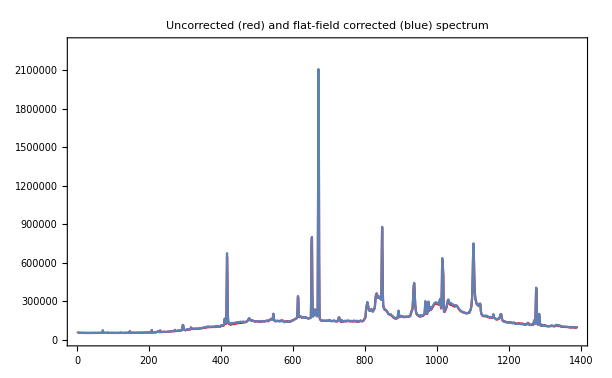

```mathematica
plot=ListPlot[objspec=Drop[Transpose[{Range[nXpixels],Total[Take[objdata,1;;nYpixels]]}],0],Joined->True, 
Axes-> False,Frame->True,  PlotStyle->Red,PlotLabel->"Uncorrected (red) and flat-field corrected (blue) spectrum",PlotRange->{{1, nXpixels},{0, 1.1 Max[objspec⟦All,2⟧]}}];
plotnorm=ListPlot[objspecnorm=Drop[Transpose[{Range[nXpixels],Total[Take[objnorm,1;;nYpixels]]}],0],Joined->True, 
Axes-> False,Frame->True,  PlotRange->{{1, nXpixels},{0, 1.1 Max[objspecnorm⟦All,2⟧]}}];
Show[plot, plotnorm]
```

## 3. Wavelength calibration

In this section a wavelength calibration function is obtained. This function relates the pixels to wavelengths. Because the Neon lines are slanted the wavelength function λ(x) is a function of y as well.

Below the calibration spectrum is plotted for every vertical pixel row (in arbitrary units). This is for demo only, but it shows that the wavelenth function should also depend on the y pixel value.

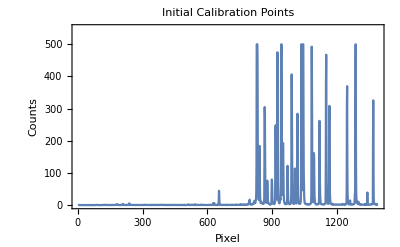

```mathematica
maxcalflux=500;
calspec=Table[Transpose[{Range[nXpixels],maxcalflux(caldata⟦i⟧-Min[caldata⟦i⟧])/(Max[caldata⟦i⟧]-Min[caldata⟦i⟧])}],{i,1,nYpixels}];
Manipulate[ListLinePlot[calspec⟦i⟧,Frame->True,Axes->False,PlotRange->{{1,nXpixels},{0,600}},FrameLabel->"x pixel"],{{i,1,"y pixel"},1,nYpixels,1,Appearance->"Labeled"}]
calplot=ListLinePlot[calspec⟦Round[nYpixels/2]⟧,Frame->True,Axes->False,PlotLabel->"Initial Calibration Points",FrameLabel->{"Pixel","Counts"},PlotRange->{{1,nXpixels},{0,1.1maxcalflux}}]
```

In this section we try to find initial calibration points. This is done  by setting up the approximate dispersion relation to predict the expected neon line positions.
listNeon contains all carefully selected isolated neon and argon lines which give an optimal fit.

Then for every y pixel row a fit is made to find the location of the initial calibration points in the spectrum. This fit makes use of the approximate dispersion relation to determine a first guess. 
The fit results are shown for display.

```mathematica
(* This should give the position of the first strong line in the center of the plot. *)
xλcenter=Position[caldata⟦Round[(nYpixels-1)/2]⟧⟦600;;700⟧,Max[caldata⟦Round[(nYpixels-1)/2]⟧⟦600;;700⟧]]⟦1,1⟧+599;
Print["Max flux at center line = ",caldata⟦Round[(nYpixels-1)/2]⟧⟦xλcenter⟧]
Print["λstart = ",λstart=5400.5616-2.537(-1+xλcenter)-0.000022 (-1+xλcenter)^2]
xpixel[λ_]:=Round[Replace[x,Solve[λ==λstart+2.541(-1+x)+0.00002 (-1+x)^2,x]⟦2⟧]]

listNeon={(*next 4 lines are Argon *){3948.979,1},{4044.418,1},{4158.590,3},{4259.362,3},{5037.7512,2},(*{5080.383,1},*){5116.5032,1},{5400.5616,10},(*next line is overexposed, and omitted *)(*{5852.488,500},*){5944.834,100},{6217.281,150},(*{6266.495,150},*){6334.428,100},(*{6402.25,100},*){6598.953,150},{6678.276,90},{6717.043,20},{6929.467,100},{7032.4131,10},{7173.9381,10},{7245.1666,100}};
callist=listNeon;
em1[a_,b_,c_,d_,x_]:= d+a ⅇ^(-((x-c)/b)^2)

linepos=Transpose[{Table[i,{i,Length[callist]}],Map[xpixel,callist⟦All,1⟧],callist⟦All,1⟧,callist⟦All,2⟧}];
weights=sigxcal=e1=topcal=pixcal=width=background=calObs = Range[Length[linepos]];
disppar1y=disppar2y=disppar3y=disppar4y=objspectra=calspectra=Range[nYpixels];
```

Max flux at center line = 6036.

λstart = 3734.52

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ypixel = 1 Fitting line 1 85 3948.98, pix = 116.835 ± 4286.8,  Top = 96.6,  Width = 531.74, weight = 5.44169×10^-8

ypixel = 1 Fitting line 2 123 4044.42, pix = 124.905 ± 0.251,  Top = 0.5,  Width = 1.01, weight = 15.8246

ypixel = 1 Fitting line 3 168 4158.59, pix = 168.651 ± 0.376,  Top = 0.4,  Width = 1.83, weight = 7.0663

ypixel = 1 Fitting line 4 207 4259.36, pix = 208.978 ± 0.103,  Top = 2.4,  Width = 1.45, weight = 94.1694

ypixel = 1 Fitting line 5 512 5037.75, pix = 513.34 ± 0.099,  Top = 2.,  Width = 1.2, weight = 102.197

ypixel = 1 Fitting line 6 543 5116.5, pix = 543.952 ± 0.17,  Top = 1.2,  Width = 1.35, weight = 34.5597

ypixel = 1 Fitting line 7 653 5400.56, pix = 654.868 ± 0.024,  Top = 38.7,  Width = 1.37, weight = 1705.73

ypixel = 1 Fitting line 8 865 5944.83, pix = 866.741 ± 0.05,  Top = 248.6,  Width = 1.82, weight = 398.063

ypixel = 1 Fitting line 9 971 6217.28, pix = 972.572 ± 0.063,  Top = 88.3,  Width = 1.92, weight = 255.666

ypixel = 1 Fitting line 10 1016 6334.43, pix = 1018. ± 0.055,  Top = 229.3,  Width = 1.81, weight = 333.89

ypixel = 1 Fitting line 11 1118 6598.95, pix = 1120.43 ± 0.052,  Top = 195.5,  Width = 1.69, weight = 371.058

ypixel = 1 Fitting line 12 1149 6678.28, pix = 1151.08 ± 0.047,  Top = 363.2,  Width = 1.56, weight = 451.138

ypixel = 1 Fitting line 13 1164 6717.04, pix = 1166.07 ± 0.038,  Top = 245.7,  Width = 1.45, weight = 677.937

ypixel = 1 Fitting line 14 1246 6929.47, pix = 1248.01 ± 0.022,  Top = 310.1,  Width = 1.31, weight = 2040.81

ypixel = 1 Fitting line 15 1286 7032.41, pix = 1287.62 ± 0.036,  Top = 552.1,  Width = 1.45, weight = 786.982

ypixel = 1 Fitting line 16 1340 7173.94, pix = 1341.97 ± 0.013,  Top = 32.4,  Width = 1.16, weight = 6160.77

ypixel = 1 Fitting line 17 1368 7245.17, pix = 1369.26 ± 0.01,  Top = 260.8,  Width = 1.25, weight = 9592.84

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit :: cvmit will be suppressed during this calculation.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

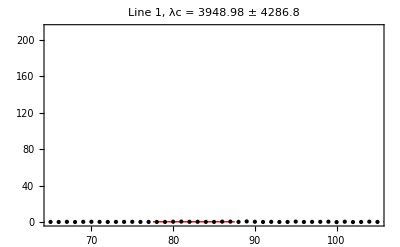
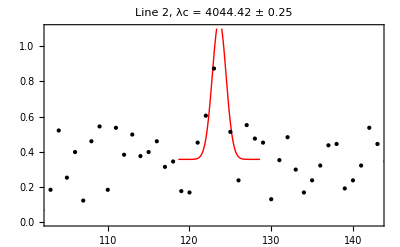
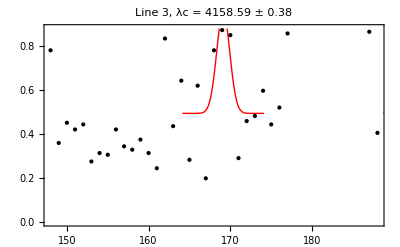
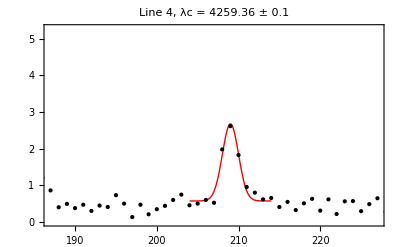
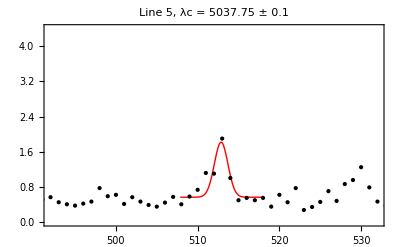
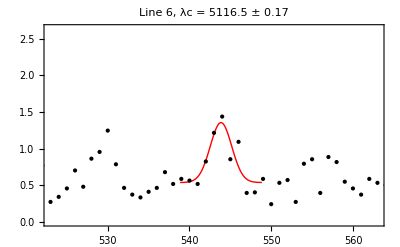
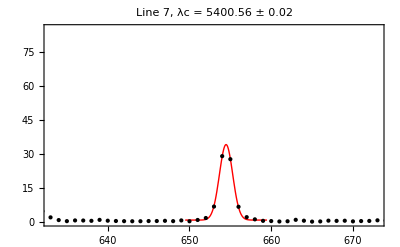
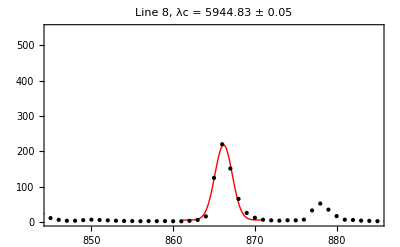

```mathematica
par1[a_,b_]:=a + b( x-1);
par2[a_,b_,c_]:=a + b( x-1) +c(x-1)^2;
par3[a_,b_,c_,d_]:=a + b( x-1)+ c (x-1)^2+d (x-1)^3
par4[a_,b_,c_,d_,e_]:=a + b( x-1)+ c (x-1)^2+d (x-1)^3+e(x-1)^4
xrange=6;
Do[Do[e1⟦i⟧=NonlinearModelFit[calspec⟦y⟧⟦linepos⟦i,2⟧-xrange;;linepos⟦i,2⟧+xrange⟧,em1[a,b,c,d,x],{{a,calspec⟦y⟧⟦linepos⟦i,2⟧,2⟧},{b,2},{c,linepos⟦i,2⟧},{d,0}},x];calObs⟦i⟧={e1⟦i⟧["BestFitParameters"]⟦3,2⟧,linepos⟦i,3⟧};
If[y==1 (*||y==nYpixels*),Print["ypixel = ",y," Fitting line ",i," ",linepos⟦i,2⟧," ",callist⟦i,1⟧,", pix = ",pixcal⟦i⟧=e1⟦i⟧["BestFitParameters"]⟦3,2⟧," ± ",sigxcal⟦i⟧ =Round[1000e1⟦i⟧["ParameterErrors"]⟦3⟧]/1000., ",  Top = ",topcal⟦i⟧=Round[10 e1⟦i⟧["BestFitParameters"]⟦1,2⟧]/10.,",  Width = ",width⟦i⟧=Round[100e1⟦i⟧["BestFitParameters"]⟦2,2⟧]/100.,", weight = ", weights⟦i⟧=1/e1⟦i⟧["ParameterErrors"]⟦3⟧^2]];
,{i,1,Length[linepos]}];
disppar1y⟦y⟧=NonlinearModelFit[calObs,par1[a, b],{a,b},x,Weights->weights];
disppar2y⟦y⟧=NonlinearModelFit[calObs,par2[a, b,c],{a,b,c},x,Weights->weights];
disppar3y⟦y⟧=NonlinearModelFit[calObs,par3[a, b,c,d],{a,b,c,d},x,Weights->weights];
disppar4y⟦y⟧=NonlinearModelFit[calObs,par4[a, b,c,d,e],{a,b,c,d,e},x,Weights->weights],
{y,1,nYpixels}];

Table[Plot[e1⟦i⟧[x],{x,e1⟦i⟧["BestFitParameters"]⟦3,2⟧-5,e1⟦i⟧["BestFitParameters"]⟦3,2⟧+5},Frame->True,Axes->False,PlotRange->{{linepos⟦i,2⟧-20,linepos⟦i,2⟧+20},{0,Abs[2.2topcal⟦i⟧]}},Epilog->Point[calspec⟦nYpixels⟧],PlotStyle->{Red,Thick},PlotLabel->"Line "<>ToString[i]<>", λc = "<>ToString[linepos⟦i,3⟧]<>" ± "<>ToString[Round[100sigxcal⟦i⟧]/100.]],
{i,Length[linepos]}]
Show[calplot,Epilog->{PointSize[Medium],Point[Transpose[{pixcal,topcal}]]}]
callist⟦All,1⟧;
pixcal;
sigxcal;
err=disp sigxcal;
(* err=callist⟦All,1⟧ sigxcal/pixcal;*)
```

Average wavelength range linear fit is 3712.89 till 7301.38

Average wavelength range quadratic fit is 3736.42 till 7302.53

Wavelength range cubic fit is 3728.51 till 7302.86

Wavelength range quartic fit is 3733.3 till 7303.02

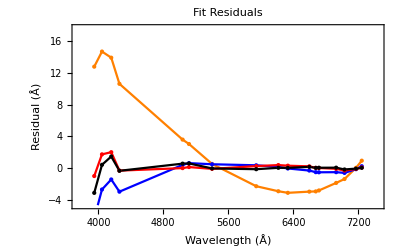

```mathematica
j=Round[(nYpixels-1)/2];

linear=Plot[Normal[disppar1y⟦j⟧],{x,1,nXpixels},FrameLabel->{"Pixel","Wavelength (A)"},Frame->True,Epilog->{Point[calObs]},PlotLabel->"Linear fit"];
quadratic=Plot[Normal[disppar2y⟦j⟧],{x,1,nXpixels},FrameLabel->{"Pixel","Wavelength (A)"},Frame->True,Epilog->{Point[calObs]},PlotLabel->"Quadratic fit"];
cubic=Plot[Normal[disppar3y⟦j⟧],{x,1,nXpixels},FrameLabel->{"Pixe.l","Wavelength (A)"},Frame->True,Epilog->{Point[calObs]},PlotLabel->"Cubic fit"];
quartic=Plot[Normal[disppar4y⟦j⟧],{x,1,nXpixels},FrameLabel->{"Pixel","Wavelength (A)"},Frame->True,Epilog->{Point[calObs]},PlotLabel->"Quartic fit"];

resid1=Transpose[{linepos⟦All,3⟧,disppar1y⟦j⟧["FitResiduals"]}];
resid1e=Transpose[{Transpose[{linepos⟦All,3⟧,disppar1y⟦j⟧["FitResiduals"]}],MapThread[ErrorBar,{err}]}];
resid2=Transpose[{linepos⟦All,3⟧,disppar2y⟦j⟧["FitResiduals"]}];
resid2e=Transpose[{Transpose[{linepos⟦All,3⟧,disppar2y⟦j⟧["FitResiduals"]}],MapThread[ErrorBar,{err}]}];
resid3=Transpose[{linepos⟦All,3⟧,disppar3y⟦j⟧["FitResiduals"]}];
resid3e=Transpose[{Transpose[{linepos⟦All,3⟧,disppar3y⟦j⟧["FitResiduals"]}],MapThread[ErrorBar,{err}]}];
resid4=Transpose[{linepos⟦All,3⟧,disppar4y⟦j⟧["FitResiduals"]}];
resid4e=Transpose[{Transpose[{linepos⟦All,3⟧,disppar4y⟦j⟧["FitResiduals"]}],MapThread[ErrorBar,{err}]}];

Table[{resid1⟦All,{1,2}⟧//TableForm,resid2⟦All,{1,2}⟧//TableForm,resid3⟦All,{1,2}⟧//TableForm,resid4⟦All,{1,2}⟧//TableForm},{1}];
res1=ErrorListPlot[resid1e,Frame->True,FrameLabel->{"Wavelength (Å)","Residual (Å)"},PlotRange->{{linepos⟦1,3⟧-500,linepos⟦-1,3⟧+500},{1.5Min[resid1⟦All,2⟧],1.5 Max[resid1⟦All,2⟧]}},PlotStyle->Orange,Joined->True,PlotLabel->"Linear fit residuals",Epilog->{PointSize[Large],Orange,Point[resid1]}];
res2=ErrorListPlot[resid2e,Frame->True,FrameLabel->{"Wavelength (Å)","Residual (Å)"},PlotRange->{{linepos⟦1,3⟧-500,linepos⟦-1,3⟧+500},{2Min[resid2⟦All,2⟧],3 Max[resid2⟦All,2⟧]}},PlotStyle->Blue,Joined->True,PlotLabel->"Quadratic fit residuals",Epilog->{PointSize[Large],Blue,Point[resid2]}];
res3=ErrorListPlot[resid3e,Frame->True,FrameLabel->{"Wavelength (Å)","Residual (Å)"},PlotRange->{{linepos⟦1,3⟧-500,linepos⟦-1,3⟧+500},{3.5Min[resid3⟦All,2⟧],3.5 Max[resid3⟦All,2⟧]}},PlotStyle->Red,Joined->True,PlotLabel->"Cubic fit residuals",Epilog->{PointSize[Large],Red,Point[resid3]}];
res4=ErrorListPlot[resid4e,Frame->True,FrameLabel->{"Wavelength (Å)","Residual (Å)"},PlotRange->{{linepos⟦1,3⟧-500,linepos⟦-1,3⟧+500},{3.5Min[resid4⟦All,2⟧],3.5 Max[resid4⟦All,2⟧]}},PlotStyle->Black,Joined->True,PlotLabel->"Quartic fit residuals",Epilog->{PointSize[Large],Black,Point[resid4]}];

Table[{res1,res2,res3,res4},{1}];
(*Table[{res1,res2},{1}]*)
Print["Average wavelength range linear fit is ",Normal[disppar1y⟦j⟧]/.x->1, " till ",Normal[disppar1y⟦j⟧]/.x->nXpixels]
Print["Average wavelength range quadratic fit is ",Normal[disppar2y⟦j⟧]/.x->1, " till ",Normal[disppar2y⟦j⟧]/.x->nXpixels]
Print["Wavelength range cubic fit is ",Normal[disppar3y⟦j⟧]/.x->1, " till ",Normal[disppar3y⟦j⟧]/.x->nXpixels]
Print["Wavelength range quartic fit is ",Normal[disppar4y⟦j⟧]/.x->1, " till ",Normal[disppar4y⟦j⟧]/.x->nXpixels]
Sqrt[Total[resid1⟦All,2⟧^2]/Length[resid1⟦All,2⟧]];
Sqrt[Total[resid2⟦All,2⟧^2]/Length[resid2⟦All,2⟧]];
Sqrt[Total[resid3⟦All,2⟧^2]/Length[resid3⟦All,2⟧]];
Sqrt[Total[resid4⟦All,2⟧^2]/Length[resid4⟦All,2⟧]];

ErrorListPlot[{resid1e,resid2e,resid3e,resid4e},Joined->True,Frame->True,PlotStyle->{Orange,Blue,Red,Black},PlotRange->{{resid1e⟦1,1,1⟧-200,resid1e⟦-1,1,1⟧+200},{1.5Min[resid1e⟦All,1,2⟧],1.2Max[resid1e⟦All,1,2⟧]}},Epilog->{{PointSize[Medium],Orange,Point[resid1]},{PointSize[Medium],Blue,Point[resid2]},{PointSize[Medium],Red,Point[resid3]},{PointSize[Medium],Black,Point[resid4]}},PlotLabel->"Fit Residuals",FrameLabel->{"Wavelength (Å)","Residual (Å)"}]

disppar1y⟦j⟧["ANOVATable"];
disppar2y⟦j⟧["ANOVATable"];
disppar3y⟦j⟧["ANOVATable"];
disppar4y⟦j⟧["ANOVATable"];
```

The conclusion for the results above is that the best fit for a given y-row is given by the function λ(x) = a0 + a1(x-1) + a2(x-1)^2+a3(x-1)^3+a4(x-1)^4
The y-dependence of the fit parameters (a0...a4)  for LISA spectra is: 
                    a0(y) = a40+ a40(y-1)
                    a1(y) = a41+ a41(y-1)
                    a2(y) = a42+ a42(y-1)
                    a3(y) = a43+ a43(y-1)
                    a4(y) = a44+ a44(y-1)
Below the best values for the additional parameters are found.

```mathematica
(* a20=Table[disppar2y⟦y⟧⟦1,2,1,2⟧, {y,1,nYpixels}];ListPlot[a20];
a21=Table[disppar2y⟦y⟧⟦1,2,2,2⟧, {y,1,nYpixels}];ListPlot[a21];
a22=Table[disppar2y⟦y⟧⟦1,2,3,2⟧, {y,1,nYpixels}];ListPlot[a22];*)
a40=Table[disppar4y⟦y⟧⟦1,2,1,2⟧, {y,1,nYpixels}];ListPlot[a40];
a41=Table[disppar4y⟦y⟧⟦1,2,2,2⟧, {y,1,nYpixels}];ListPlot[a41];
a42=Table[disppar4y⟦y⟧⟦1,2,3,2⟧, {y,1,nYpixels}];ListPlot[a42];
a43=Table[disppar4y⟦y⟧⟦1,2,4,2⟧, {y,1,nYpixels}];ListPlot[a43];
a44=Table[disppar4y⟦y⟧⟦1,2,5,2⟧, {y,1,nYpixels}];ListPlot[a44];

a40par1=NonlinearModelFit[a40,par1[a, b],{a,b},x]
resida40y=Transpose[{Range[nYpixels],a40par1["FitResiduals"]}];
ListPlot[resida40y,PlotLabel->"a40 Linear fit"];
a41par1=NonlinearModelFit[a41,par1[a, b],{a,b},x]
resida41y=Transpose[{Range[nYpixels],a41par1["FitResiduals"]}];
ListPlot[resida41y,PlotLabel->"a41 Linear fit"];
a42par1=NonlinearModelFit[a42,par1[a, b],{a,b},x]
resida42y=Transpose[{Range[nYpixels],a42par1["FitResiduals"]}];
ListPlot[resida42y,PlotLabel->"a42 Linear fit"];
a43par1=NonlinearModelFit[a43,par1[a, b],{a,b},x]
resida43y=Transpose[{Range[nYpixels],a43par1["FitResiduals"]}];
ListPlot[resida43y,PlotLabel->"a43 Linear fit"];
a44par1=NonlinearModelFit[a44,par1[a, b],{a,b},x]
resida44y=Transpose[{Range[nYpixels],a44par1["FitResiduals"]}];
ListPlot[resida44y,PlotLabel->"a44 Linear fit"];
```

FittedModel[3730.71+0.0104355 (-1+x)]

FittedModel[2.53542-0.0000549615 (-1+x)]

FittedModel[0.0000458536+1.4581×10^-7 (-1+x)]

FittedModel[-3.62431×10^-8-1.37833×10^-10 (-1+x)]

FittedModel[1.49245×10^-11+4.42339×10^-14 (-1+x)]

```mathematica
(* Final Wavelength calibration function *)
λ[x_,y_]:=a40par1[y]+a41par1[y](x-1)+a42par1[y](x-1)^2+a43par1[y](x-1)^3+a44par1[y](x-1)^4
(* Manipulate[ListLinePlot[λ[Range[nXpixels],y],Frame->True,Axes->False,PlotRange->{{1,nXpixels},{3700,7500}}],{y,1,nYpixels,1,Appearance->"Labeled"}]*)
```

Now we have obtained the final wavelength calibration function. Below the object spectrum is plotted with the pixels converted into wavelengths (for each y row). 
For display only.

```mathematica
(* Example plot at given row *)
(* Optional smoothing *)
Manipulate[
ListLinePlot[Transpose[{λ[Range[sm/2,nXpixels-sm/2],y], MovingAverage[caldata⟦y⟧,sm]}],(* PlotRange->{{λ[Range[nXpixels],j]⟦1⟧,λ[nXpixels,j]},{280,400}} *)PlotRange->{{4000,6650},{0,20000}},Frame->True,Axes->False,PlotLabel->"Neon spectrum",FrameLabel->{"Wavelength (Å)","Counts"}],{y,1,nYpixels,1,Appearance->"Labeled"},{sm,2,20,2,Appearance->"Labeled"}];
Manipulate[
ListLinePlot[Transpose[{λ[Range[sm/2,nXpixels-sm/2],y], MovingAverage[objdata⟦y⟧,sm]}],(* PlotRange->{{λ[Range[nXpixels],j]⟦1⟧,λ[nXpixels,j]},{280,1000}} *)PlotRange->{{4000,7300},{0,50000}},Frame->True,Axes->False,PlotLabel->"Object spectrum",FrameLabel->{"Wavelength (Å)","Counts"}],{y,1,nYpixels,1,Appearance->"Labeled"},{sm,2,20,2,Appearance->"Labeled"}]
```

Range::range: Range specification in Range[1, -1 + nXpixels] does not have appropriate bounds.

Part::partd: Part specification objdata ⟦ 104 ⟧ is longer than depth of object.

MovingAverage::vecmat: Argument objdata ⟦ 104 ⟧ at position 1 is neither a non-empty vector nor a non-empty matrix.

Transpose::nmtx: The first two levels of {λ[Range[1, -1 + nXpixels], 104], MovingAverage[objdata ⟦ 104 ⟧, 2]} cannot be transposed.

MovingAverage::vecmat: Argument objdata ⟦ 104 ⟧ at position 1 is neither a non-empty vector nor a non-empty matrix.

Transpose::nmtx: The first two levels of {λ[Range[1, -1 + nXpixels], 104], MovingAverage[objdata ⟦ 104 ⟧, 2]} cannot be transposed.

Range::range: Range specification in Range[1., -1. + nXpixels] does not have appropriate bounds.

MovingAverage::vecmat: Argument objdata ⟦ 104 ⟧ at position 1 is neither a non-empty vector nor a non-empty matrix.

General::stop: Further output of MovingAverage :: vecmat will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {λ[Range[1., -1. + nXpixels], 104.], MovingAverage[objdata ⟦ 104 ⟧, 2.]} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

Range::range: Range specification in Range[1., -1. + nXpixels] does not have appropriate bounds.

General::stop: Further output of Range :: range will be suppressed during this calculation.

ListLinePlot::lpn: Transpose[{λ[Range[1., -1. + nXpixels], 104.], MovingAverage[objdata ⟦ 104 ⟧, 2.]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot :: lpn will be suppressed during this calculation.

## 4. Sky background removal

In this section a fit is made of the background light in the spectrum. This is then substracted from the spectrum. 
First, the spectra is converted on the same wavelength grid for every ypixel.

```mathematica
objspec=Range[nYpixels];
Do[
interp=Interpolation[Transpose[{λ[Range[1,nXpixels],y], objdata⟦y⟧}]];
objspec⟦y⟧=Transpose[{λ[Range[2,nXpixels],1],interp[λ[Range[2,nXpixels],1]]}];,
{y,1,nYpixels}]
(* ListPlot[Table[λ[1,y],{y,1,nYpixels}]]
Length[objspec⟦1⟧] *)
slice=Table[Transpose[{Range[nYpixels],Table[objspec⟦y⟧⟦x,2⟧,{y,1,nYpixels}]}],{x,1,nXpixels-1}];
Manipulate[ListLinePlot[slice⟦x⟧,PlotRange->{{1,nYpixels},{0,50000}},Frame->True,Axes->False, FrameLabel->{"Y Pixel","Counts"}],{x,1,nXpixels-1,1}]
```

Part::partd: Part specification slice ⟦ 669 ⟧ is longer than depth of object.

ListLinePlot::prng: Value of option PlotRange -> {{1, nYpixels}, {0, 50000}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: slice ⟦ 669 ⟧ is not a list of numbers or pairs of numbers.

ListLinePlot::prng: Value of option PlotRange -> {{1, nYpixels}, {0, 50000}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: slice ⟦ 669 ⟧ is not a list of numbers or pairs of numbers.

ListLinePlot::prng: Value of option PlotRange -> {{1, nYpixels}, {0, 50000}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListLinePlot :: prng will be suppressed during this calculation.

ListLinePlot::lpn: slice ⟦ 669 ⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot :: lpn will be suppressed during this calculation.

Two regions of the spectrum containing primarily background light will be selected at either side of the object light peak. Then from these background regions a fit is made that is substracted from the entire spectrum.

From the plot above select two regions of background light. In explicit: Select two regions around the peak.
ylow1 < region 1 < ylow2 and yhigh2 < region 2 < yhigh2

Fill in the values for ylow1, ylow2, yhigh1, yhigh2 below.

```mathematica
ylow1=35;ylow2=40;yhigh1=130;yhigh2=140;
line=Table[Fit[Join[slice⟦i⟧⟦ylow1;;ylow2⟧,slice⟦i⟧⟦yhigh1;;yhigh2⟧],{1,x},x],{i,1,nXpixels-1}];
ListLinePlot[specslice=slice⟦All,All,2⟧-(line/.x->Range[nYpixels]),PlotRange->{{1,nYpixels},{-100,200}},Frame->True,Axes->False,FrameLabel->{"Y Pixel","Count"},PlotLabel->"Overplot of vertical slices"]
```

In the plot below increase the values of ymin and ymax such that the flux is still at maximum.
Click the + signs next to the sliders to show the values of ymin and ymax.

Fill in the values you found for ymin and ymax below the graph.

```mathematica
Manipulate[ListLinePlot[MovingAverage[Total[Table[specslice⟦All,i⟧,{i,1,nYpixels}]⟦ymin;;ymax⟧],mv],Frame->True,Axes->False,PlotRange->{{1,nXpixels-1},{0,550000}}],{ymin,1,Round[(nYpixels-1)/2],1},{ymax,Round[(nYpixels-1)/2]-30,nYpixels,1},{mv,1,17,2}]
```

Part::take: Cannot take positions 130 through 1400 in {{1., 281.}, {2., 264.9}, {3., 283.078}, {4., 291.583}, {5., 299.6}, {6., 277.018}, {7., 267.241}, {8., 306.339}, « 35 », {44., 288.551}, {45., 337.586}, {46., 280.561}, {47., 246.014}, {48., 271.258}, {49., 262.064}, {50., 275.911}, « 151 »}.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

General::ivar: 1. is not a valid variable.

Part::take: Cannot take positions 130 through 1400 in {{1., 296.}, {2., 284.949}, {3., 277.996}, {4., 312.968}, {5., 298.302}, {6., 271.183}, {7., 263.911}, {8., 275.934}, « 35 », {44., 287.133}, {45., 272.671}, {46., 294.48}, {47., 303.903}, {48., 283.545}, {49., 276.024}, {50., 280.319}, « 151 »}.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

General::ivar: 1. is not a valid variable.

Part::take: Cannot take positions 130 through 1400 in {{1., 275.}, {2., 284.026}, {3., 285.995}, {4., 285.3}, {5., 281.274}, {6., 262.992}, {7., 274.574}, {8., 274.754}, « 35 », {44., 254.926}, {45., 279.355}, {46., 274.104}, {47., 284.176}, {48., 284.}, {49., 279.086}, {50., 259.713}, « 151 »}.

General::stop: Further output of Part :: take will be suppressed during this calculation.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

General::ivar: 1. is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

Part::take: Cannot take positions 130 through 1400 in {{1., 281.}, {2., 264.9}, {3., 283.078}, {4., 291.583}, {5., 299.6}, {6., 277.018}, {7., 267.241}, {8., 306.339}, « 35 », {44., 288.551}, {45., 337.586}, {46., 280.561}, {47., 246.014}, {48., 271.258}, {49., 262.064}, {50., 275.911}, « 151 »}.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

General::ivar: 1. is not a valid variable.

Part::take: Cannot take positions 130 through 1400 in {{1., 296.}, {2., 284.949}, {3., 277.996}, {4., 312.968}, {5., 298.302}, {6., 271.183}, {7., 263.911}, {8., 275.934}, « 35 », {44., 287.133}, {45., 272.671}, {46., 294.48}, {47., 303.903}, {48., 283.545}, {49., 276.024}, {50., 280.319}, « 151 »}.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

General::ivar: 1. is not a valid variable.

Part::take: Cannot take positions 130 through 1400 in {{1., 275.}, {2., 284.026}, {3., 285.995}, {4., 285.3}, {5., 281.274}, {6., 262.992}, {7., 274.574}, {8., 274.754}, « 35 », {44., 254.926}, {45., 279.355}, {46., 274.104}, {47., 284.176}, {48., 284.}, {49., 279.086}, {50., 259.713}, « 151 »}.

General::stop: Further output of Part :: take will be suppressed during this calculation.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

General::ivar: 1. is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

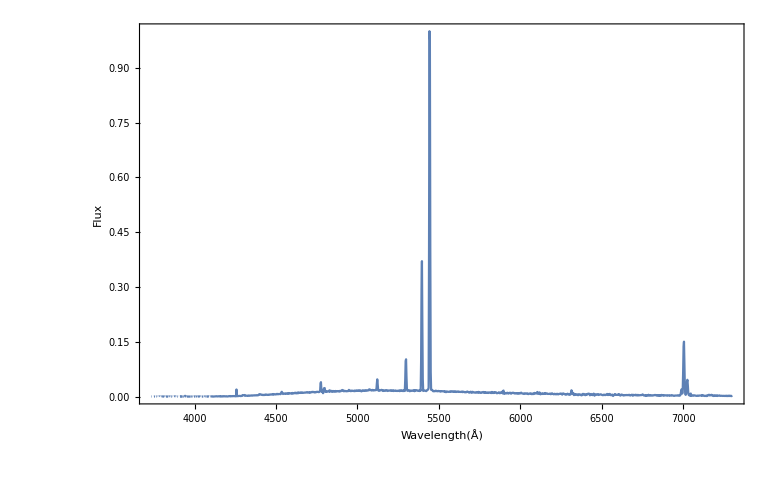

```mathematica
ymin=100;ymax=201;
specf=Transpose[{λ[Range[2,nXpixels],1],Total[Table[specslice⟦All,i⟧,{i,1,nYpixels}]⟦ymin;;ymax⟧]}];
specf[[All,2]]=specf[[All,2]]/Max[specf[[All,2]]];
plotfin=ListLinePlot[specf,Frame->True,Axes->False,PlotRange->{{specf[[1,1]],specf[[-1,1]]},{0,1}},FrameLabel->{"Wavelength(Å)","Flux"}]
```

## 5. Instrumental response correction

Here an average instrumental response function is used, based on spectra of Xi Aur (spectral type A2V) which was  divided by a published spectrum of this star with absolute fluxes, smoothed, and rebinned on the same wavelength grid as the object spectrum.

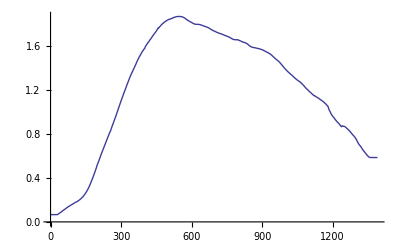

```mathematica
resp=Import["C:\\Users\\Marcella Wijngaarden\\Documents\\UvA\\Bachelorproject SN2014J in M 82\\LISAresponsefx.dat","Table"];
ListLinePlot[resp]
```

C:\Users\Marcella Wijngaarden\Dropbox\APO Waarneempracticum LISA analyse\Kriek_Ivo\eskimo_nebula_1800s (2).fit

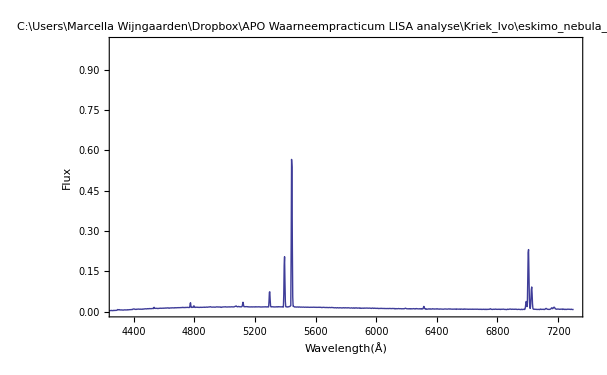

```mathematica
plotlabel=Directory[]<>"\\"<>objfile
mv=1;objspectrumfinal=MovingAverage[Transpose[{specf[[All,1]],(specf[[All,2]])/Drop[resp[[All,2]],1]}],mv];
objspectrumfinalfig=ListLinePlot[objspectrumfinal,Frame->True,Axes->False,PlotRange->{{4300,specf[[-1,1]]},{0,1}},FrameLabel->{"Wavelength(Å)","Flux"},PlotLabel->plotlabel]
```

## 6. Extract final spectrum

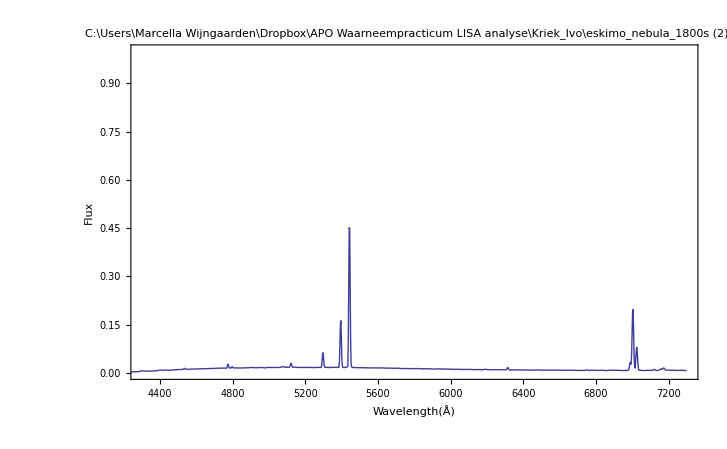

```mathematica
(* Smoothing with mv = 4 is not necessarily better *)
objspectrumfinal=MovingAverage[Transpose[{specf⟦All,1⟧,(specf⟦All,2⟧)/Drop[resp⟦All,2⟧,1]}],3];
objspectrumfinalfig = ListLinePlot[objspectrumfinal,Frame->True,Axes->False,PlotRange->{{4300,specf⟦-1,1⟧},{0,1}},FrameLabel->{"Wavelength(Å)","Flux"},PlotLabel->plotlabel]
```